```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\iT.xlsx"]
```

```mathematica
data={{2.,176.5594777562863},{1.4285714285714286,149.5596668487166},{0.8,139.93037812979054},{0.6060606060606061,134.63311209439533},{0.4,125.1571069469836}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\iT1.xlsx"]
```

```mathematica
data1={{2.,2226.371951219485},{1.4285714285714286,1041.2309885931509},{1.,468.10897435897357},{0.8,367.0827747989273},{0.6060606060606061,280.29042988741037},{0.4,225.38580246913577}};
```

```mathematica
Import["C:\\Users\\Juntao Yu\\Desktop\\Enzyme Activity\\iT2.xlsx"]
```

```mathematica
data2={{2.,1131.585743801647},{1.,789.1750720461067},{0.8,918.9387583892579},{0.6060606060606061,504.31629834254056}};
```

```mathematica
a1=LinearModelFit[data,x,x]
```

FittedModel[114.583+29.2142 x]

```mathematica
b1=LinearModelFit[data1,x,x]
c1=LinearModelFit[data2,x,x]
```

FittedModel[-537.546+1256.49 x]

FittedModel[444.965+355.001 x]

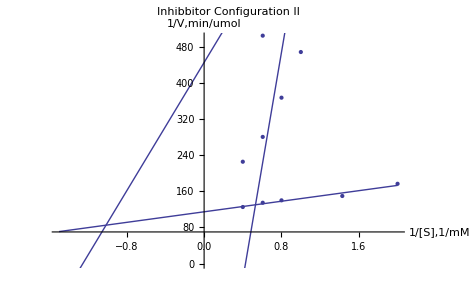

```mathematica
Show[Plot[a1[x],{x,-1.5,2}],Plot[b1[x],{x,-1.5,2}],Plot[c1[x],{x,-1.5,2}],ListPlot[data],ListPlot[data1],ListPlot[data2],PlotRange->{0,500},PlotLabel->"Inhibbitor Configuration II",AxesLabel->{"1/[S],1/mM","1/V,min/umol"}]
```